# Simulations

## Parameters

```mathematica
ClearAll[cg,Vg,R, δlac, mE,y,ξunit, Nf, Nr];
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[9/10,"Nanograms"]Quantity["Days"/"Milliliters"]);
```

## Functions

Polytope

```mathematica
ClearAll[vo,vl,vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal]
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;
vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

vgMinGlobal = 0;
vgMaxGlobal[ξ_] :=   Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(1+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];
vertexes[ξ_]:=If[vatpMaxGlobal[ξ]>Nr * R,
{{vatpMinGlobal,vgMinGlobal},{Nf * vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]},{(1 + Nr)R,R/Nf}},
{{vatpMinGlobal,vgMinGlobal},{Nf * vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]}}]
```

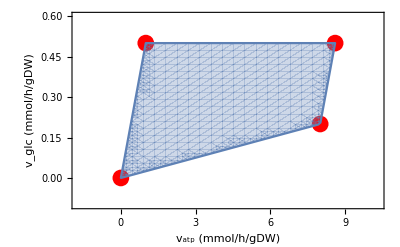

```mathematica
ClearAll[polytope,showPolytope];
polytope[ξ_][vg_,vatp_]:=Boole[vatpMinLocal[vg] ≤ vatp ≤ vatpMaxLocal[vg] ∧ vgMinLocal[vatp]≤vg≤vgMaxLocal[ξ][vatp]];
showPolytope[ξ_] := Module[{},
Show[
ListPlot[vertexes[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,0,vatpMaxGlobal[ξ]},{vg,0,vgMaxGlobal[ξ]}]]];
showPolytope[2]
```

Growth Functions

```mathematica
ClearAll[δ,λ,λmax]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][0.,vatpMaxGlobal[ξ]]
```

Probability Distribution and  Integrals

```mathematica
ClearAll[generalIntegral,distribution,totalIntegral, totalIntegralValue, integrateFixingVatp];

(* the distribution of the Probability inside the politope*)
distribution[ξ_,β_,vatp_] := Exp[-β y(vatpMaxGlobal[ξ]-vatp)];

(* General Integral *) 
generalIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]:=Module[{int0,int1,lb,ub},
If[atplb≥atpub,
0,
If[β>0,
Simplify@Integrate[distribution[ξ,β,vatp]fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals],
Simplify@Integrate[fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals]
]
]
];

(* Total Integral *)
totalIntegral[fun_, β_,ξ_] := generalIntegral[fun, β,ξ,{vatpMinGlobal,vatpMaxGlobal[ξ]},
{{ξ0,vatp} ↦ vgMinLocal[vatp],{ξ0,vatp}↦ vgMaxLocal[ξ][vatp]} ];

integrateFixingVatp[fun_,β_,ξ_, vatp_] := Module[{},
Integrate[distribution[ξ,β,vatp]*fun[vg,vatp],{vg,vgMinLocal[vatp],vgMaxLocal[ξ][vatp]}, Assumptions-> vatp ∈Reals]
];

totalIntegralValue[β_,ξ_] := totalIntegral[{cg,vatp} ↦ 1,β,ξ];
```

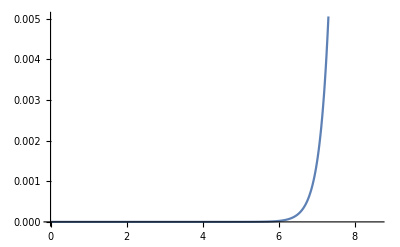

```mathematica
showDistribution := Plot[distribution[2,1000,x],{x,0,vatpMaxGlobal[2]}];
showDistribution
```

Expected values

```mathematica
ClearAll[expZ,expVatp,expVg,expVl];
expZ[β_,ξ_, norm_] :=totalIntegral[{vg,vatp} ↦ 1,β,ξ ]/norm;
expVatp[β_,ξ_, z_] := Module[{},
If[β == ∞,
vatpMaxGlobal[ξ],
 totalIntegral[{vg,vatp} ↦ vatp, β,ξ ]/z]
];
expVg[β_,ξ_, z_] := Module[{},
If[β == ∞,
vgMaxGlobal[ξ],
 totalIntegral[{vg,vatp} ↦ vg, β,ξ]/z]
];
expVl[β_,ξ_,z_] := (expVatp[β,ξ,z] - expVg[β,ξ,z] * Nf*(1+ Nr))/Nr;
expV0[β_,ξ_,z_] := Min[ Nf * expVg[β,ξ,z],R];
```

Variances and covariances

```mathematica
ClearAll[pVatp,pVg,pVgVatp]
pVatp[β_,ξ_,vatp0_] := totalIntegral[{vg,vatp} ↦ DiracDelta[vatp - vatp0],β,ξ]/totalIntegralValue[β,ξ];
pVgVatp[β_,ξ_,vatp0_,vg0_] := If[vgMinLocal[vatp0] ≤ vg0 ≤ vgMaxLocal[ξ][vatp0],
pVatp[β,ξ,vatp0]/(vgMaxLocal[ξ][vatp0] - vgMinLocal[vatp0]),
0
];
pVg[β_,ξ_,vg0_] := Integrate[pVgVatp[β,ξ,vatp,vg0],{vatp,1,10}];
```

```mathematica
pVatpTest[β_,ξ_,vatp_] := integrateFixingVatp[{vg,vatp} ↦ 1,ξ,β,vatp]//N
```

```mathematica
(* Test *)
Module [{ξ,β, testVatp, testVg},
ξ = 2;
β = 2;
Print[Style["Total tests", 35]];
Print[Style["Parameters: ", 20, Red]];
Print["Glucose in feed (cg): ", cg//N];
Print["Universal max glc uptake (Vg): ", Vg//N];
Print["Universal max respiration (R): ", R//N];
Print["Date rate doto lactate (δlac): ", δlac//N];
Print["Maintenance ATP demand (mE): ", mE//N];
Print["Units of atp needed to produce a unit of biomass (y): ", y//N];
Print["Stoichiometric coeficient of fermentation (Nf): ", Nf//N];
Print["Stoichiometric coeficient of respiration (Nr): ", Nr//N];
Print["Units of ξ (ξunit)", ξunit//N];
Print["Number of maintained cells per unit of fresh culture per unit of time (ξ): ", ξ//N];
Print["\"Heterogenity coeficient\" (β): ", β//N];
Print[""];

Print[Style["Polytope: ", 20, Red]];
Print["Global min vatp value (vatpMinGlobal): ", vatpMinGlobal//N];
Print["Global max vatp value (vatpMaxGlobal[ξ_]): ", vatpMaxGlobal[ξ]//N];
Print["Local min vatp value (vatpMinLocal[vg_]) at vgMaxGlobal/2: ", vatpMinLocal[vgMaxGlobal[ξ]/2]//N];
Print["Local max vatp value (vatpMaxLocal[vg_]) at vgMaxGlobal/2: ", vatpMaxLocal[vgMaxGlobal[ξ]/2]//N];
Print["Global min vg value (vgMinGlobal): ", vgMinGlobal//N];

Print["Global max vg value (vgMaxGlobal[ξ_]): ", vgMaxGlobal[ξ]//N];
Print["Local min vg value (vgMinLocal[vatp_]) at vatpMaxGlobal/2: ", vgMinLocal[vatpMaxGlobal[ξ]/2]//N];
Print["Local max vg value (vgMaxLocal[ξ_][vatp_]) at vatpMaxGlobal/2: ", vgMaxLocal[ξ][vatpMaxGlobal[ξ]/2]//N];
Print["Polytope vertexes (vertexes[ξ_]): ", vertexes[ξ]//N];
Print[showPolytope[2]];
Print[""];

Print[Style["Probability Distribution and integrals:", 20, Red]];
Print["Pribability distribution ( Exp[-β y(vatpMaxGlobal[ξ]-vatp)])"];
Print["Evaluated at vatpMaxGlobal/2: ", distribution[2,2,vatpMaxGlobal[2]/2]//N];
Print[showDistribution]

]
```

Total tests

Parameters:

Glucose in feed (cg): 15.

Universal max glc uptake (Vg): 0.5

Universal max respiration (R): 0.4

Date rate doto lactate (δlac): 0.0011

Maintenance ATP demand (mE): 1.

Units of atp needed to produce a unit of biomass (y): 0.00409938

Stoichiometric coeficient of fermentation (Nf): 2.

Stoichiometric coeficient of respiration (Nr): 19.

Units of ξ (ξunit)0.0462963

Number of maintained cells per unit of fresh culture per unit of time (ξ): 2.

"Heterogenity coeficient" (β): 2.

Polytope:

Global min vatp value (vatpMinGlobal): 0.

Global max vatp value (vatpMaxGlobal[ξ_]): 8.6

Local min vatp value (vatpMinLocal[vg_]) at vgMaxGlobal/2: 0.5

Local max vatp value (vatpMaxLocal[vg_]) at vgMaxGlobal/2: 8.1

Global min vg value (vgMinGlobal): 0.

Global max vg value (vgMaxGlobal[ξ_]): 0.5

Local min vg value (vgMinLocal[vatp_]) at vatpMaxGlobal/2: 0.1075

Local max vg value (vgMaxLocal[ξ_][vatp_]) at vatpMaxGlobal/2: 0.5

Polytope vertexes (vertexes[ξ_]): {{0.,0.},{1.,0.5},{8.6,0.5},{8.,0.2}}

-Graphics-

Probability Distribution and integrals:

Pribability distribution ( Exp[-β y(vatpMaxGlobal[ξ]-vatp)])

Evaluated at vatpMaxGlobal/2: 0.96536

-Graphics-